```mathematica
f2[x_,y_]:=((3+6x y+(x y)^2 )/(2+5x y+(x y)^2))^2-(3/2)^2
```

```mathematica
f[x_]:=((3+6x^2+x ^4 )/(2+5x^2 +x^4))^2-(3/2)^2
```

```mathematica
xmin=-0.1;
xmax=0.1;
```

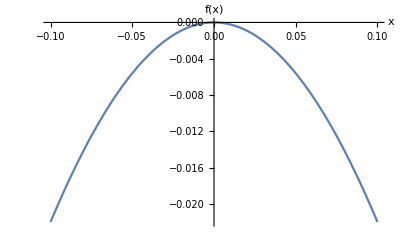

```mathematica
Plot[f[x],{x,xmin,xmax},AxesLabel->{"x","f(x)"}]
```

```mathematica
Plot3D[f2[x,y],{x,-5,5},{y,-5,5},AxesLabel->{"x","y","f(x, y)"},PlotPoints->50]
```

-Graphics3D-

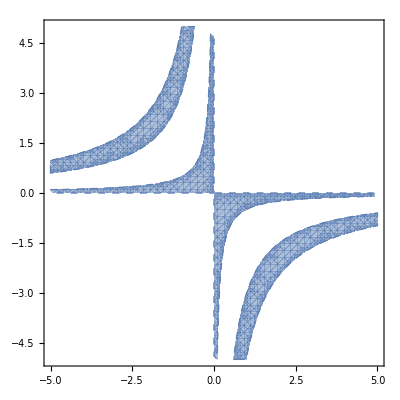

```mathematica
region=RegionPlot[f2[x,y]>0,{x,-5,5},{y,-5,5},PlotStyle->Opacity[0.5],BoundaryStyle->Directive[Thick,Dashed],PlotPoints->50]
```

```mathematica
g1[x_,y_]:=(3+6x y+(x y)^2 )
```

```mathematica
g2[x_,y_]:=(2+5x y+(x y)^2)
```

```mathematica
ProbDiff[x_,y_]:=(g1[x,y])^2-(g2[x,y])^2
```

```mathematica
Plot3D[ProbDiff[x,y],{x,-5,5},{y,-5,5},AxesLabel->{"x","y","f(x, y)"},PlotPoints->50]
```

-Graphics3D-

```mathematica
haf[matrix_?MatrixQ]:=Module[{n,h,j,copy},n=Length[matrix];

If[n==2,Return[matrix[[1,2]]]];
h=0;
For[j=2,j<=n,j++,If[matrix[[1,j]]==0,Continue[]];
copy=Delete[matrix,{{1},{j}}];
copy=Transpose[copy];
copy=Delete[copy,{{1},{j}}];
h+=matrix[[1,j]]*haf[copy];];
h]
```

```mathematica
haf[{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}]
```

3

```mathematica
Adj=0.5*{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}};
```

```mathematica
SigmaQInv=ArrayFlatten[{{IdentityMatrix[Length[Adj]],-Adj},{-Adj,IdentityMatrix[Length[Adj]]}}];
```

```mathematica
d=Dot[Transpose[{1,1,1,1,1,1,1,1}]SigmaQInv]
```

{{1,0,0,0,0,-1,-1,-1},{0,1,0,0,-1,0,-1,-1},{0,0,1,0,-1,-1,0,-1},{0,0,0,1,-1,-1,-1,0},{0,-1,-1,-1,1,0,0,0},{-1,0,-1,-1,0,1,0,0},{-1,-1,0,-1,0,0,1,0},{-1,-1,-1,0,0,0,0,1}}

```mathematica
LoopHafnian[matrix_]:=Module[{n,loopHaf,submatrix,indices,diagonalProduct},n=Length[matrix];
If[OddQ[n],Return[0]];(*Loop hafnian is zero for odd-sized matrices*)loopHaf=0;
Do[indices=Subsets[Range[n],{k}];
Do[submatrix=matrix[[indices,indices]];
diagonalProduct=Times@@(matrix[[#,#]]&/@Complement[Range[n],indices]);
If[indices==={},(*If the subset of indices is empty*)loopHaf+=diagonalProduct,(*Return the product of the diagonal elements*)loopHaf+=haf[submatrix]*diagonalProduct],{indices,Subsets[Range[n],{k}]}],{k,0,n,2}];
loopHaf]
```

6

```mathematica
LoopHafnian[{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}]
```

3

```mathematica
FillDiagonal[matrix_,weights_]:=matrix-DiagonalMatrix[Diagonal[matrix]]+DiagonalMatrix[matrix]
```

```mathematica
SigmaQInvFun[Adj_]:=ArrayFlatten[{{IdentityMatrix[Length[Adj]],-Adj},{-Adj,IdentityMatrix[Length[Adj]]}}]
```

```mathematica
DGBS[Adj_?MatrixQ,weights_,indices_]:=Exp[-Dot[Dot[Transpose[Join[weights,weights]]SigmaQInv],Join[weights,weights]]]/(FactorialProduct[indices]*Sqrt[Det[Inverse[SigmaQInvFun[Adj]]]])*Power[LoopHafnian[RepeatRowsAndColumns[FillDiagonal[Adj,weights],indices]],2]
```

```mathematica
FactorialProduct[indices_]:=Times@@(Times@@(Factorial/@ indices))
```

```mathematica
FactorialProduct[{1,2,3}]
```

12

{1,1,4,4,4,7,1,1,4,4,4,7,2,2,5,5,5,8,2,2,5,5,5,8,2,2,5,5,5,8,3,3,6,6,6,9}

```mathematica
(*Define the function*)RepeatRowsAndColumns[matrix_,repeatList_]:=Module[{n,repeatedRows,repeatedCols,newMatrix},(*Get the length of the matrix*)n=Length[matrix];
(*Check if the length of the repeat list matches the matrix dimensions*)If[Length[repeatList]!=n,Return["Error: The length of the repeat list must match the dimensions of the matrix."]];
(*Repeat the rows according to the repeat list*)repeatedRows=Flatten[Table[ConstantArray[matrix[[i]],repeatList[[i]]],{i,n}],1];
(*Repeat the columns according to the repeat list*)repeatedCols=Flatten[Table[ConstantArray[repeatedRows[[All,i]],repeatList[[i]]],{i,n}],2];
(*Construct the new matrix*)newMatrix=repeatedCols;
(*Return the new matrix*)Transpose[Partition[newMatrix,Plus@@repeatList]]]

(*Example usage*)
```

```mathematica
matrix={{1,2,3},{4,5,6},{7,8,9}};
repeatList={2,3,1};
MatrixForm[RepeatRowsAndColumns[matrix,repeatList]]
```

(1 | 1 | 2 | 2 | 2 | 3
1 | 1 | 2 | 2 | 2 | 3
4 | 4 | 5 | 5 | 5 | 6
4 | 4 | 5 | 5 | 5 | 6
4 | 4 | 5 | 5 | 5 | 6
7 | 7 | 8 | 8 | 8 | 9)

```mathematica
DGBS[Adj,{1,1,1,1},{1,1,1,1,1,1,1,1}]
```

DiagonalMatrix::vector: Argument {{0.,0.5,0.5,0.5},{0.5,0.,0.5,0.5},{0.5,0.5,0.,0.5},{0.5,0.5,0.5,0.}} at position 1 is not a non-empty vector.

{0.-5.36582 ⅈ,0.-5.36582 ⅈ,0.-5.36582 ⅈ,0.-5.36582 ⅈ,0.-5.36582 ⅈ,0.-5.36582 ⅈ,0.-5.36582 ⅈ,0.-5.36582 ⅈ}

(1 | 0 | 0 | 0 | 0. | -0.5 | -0.5 | -0.5
0 | 1 | 0 | 0 | -0.5 | 0. | -0.5 | -0.5
0 | 0 | 1 | 0 | -0.5 | -0.5 | 0. | -0.5
0 | 0 | 0 | 1 | -0.5 | -0.5 | -0.5 | 0.
0. | -0.5 | -0.5 | -0.5 | 1 | 0 | 0 | 0
-0.5 | 0. | -0.5 | -0.5 | 0 | 1 | 0 | 0
-0.5 | -0.5 | 0. | -0.5 | 0 | 0 | 1 | 0
-0.5 | -0.5 | -0.5 | 0. | 0 | 0 | 0 | 1)

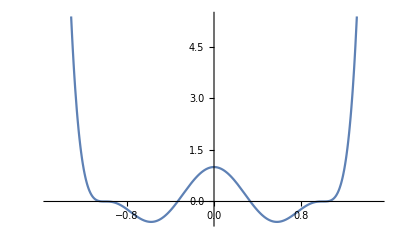

```mathematica
MatrixForm[SigmaQInvFun[Adj]]
```